# Plot Elements

## Tradition Approach

```mathematica
SeedRandom[19870716];
```

```mathematica
datah = RandomVariate[BinormalDistribution[#,{0.3,0.3},0],10]&/@{{2,3},{1,1}};
datab = RandomVariate[BinormalDistribution[#,{0.3,0.3},0],10]&/@{{4,1},{-1,4},{-1,2},{2,-1}};
dataother =  RandomVariate[BinormalDistribution[#,{0.3,0.3},0],10]&/@{{-1,-1}};
```

```mathematica
data = (datah)~Join~{Flatten[datab~Join~dataother,1]};
data2 = (datah~Join~datab)~Join~{Flatten[dataother,1]};
```

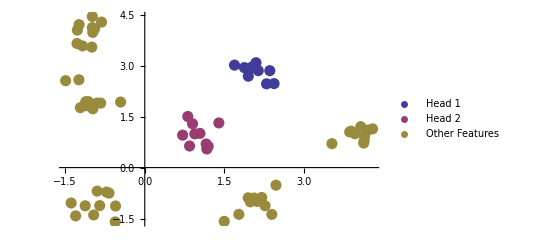

```mathematica
g11=ListPlot[data,PlotStyle->AbsolutePointSize[8],PlotLegends->Placed[PointLegend[{"Head 1","Head 2","Other Features"},LegendMarkerSize->10,LegendFunction->Frame],Above]]
```

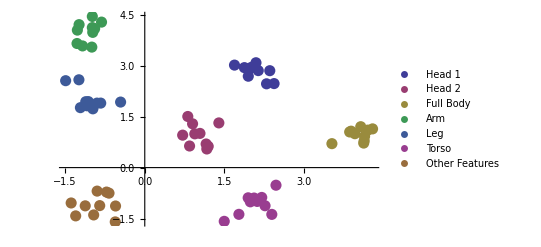

```mathematica
g2=ListPlot[data2,PlotStyle->AbsolutePointSize[8],PlotLegends->Placed[PointLegend[{"Head 1","Head 2","Full Body","Arm","Leg","Torso","Other Features"},LegendFunction->Frame],Above]]
```

```mathematica
Export["D:/final_21.pdf",g11]
```

D:/final_21.pdf

```mathematica
Export["D:/our_fea.pdf",g2]
```

D:/our_fea.pdf

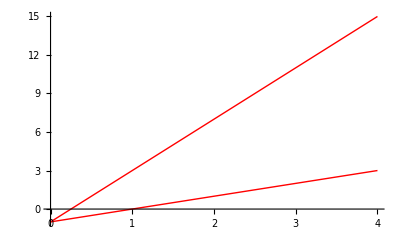

```mathematica
g12  = Plot[{4x-1,x-1},{x,0,4},PlotStyle->{Directive[Red,Thick],Directive[Red,Thick]}]
```

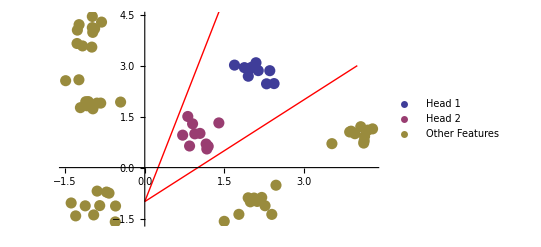

```mathematica
final12=Show[g11,g12]
```

```mathematica
Export["D:/final_12.pdf",final12]
```

D:/final_12.pdf

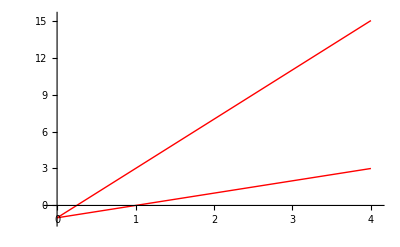

```mathematica
g3  = Plot[{4x-1,x-1},{x,0,4},PlotStyle->{Directive[Red,Thick],Directive[Red,Thick]}]
```

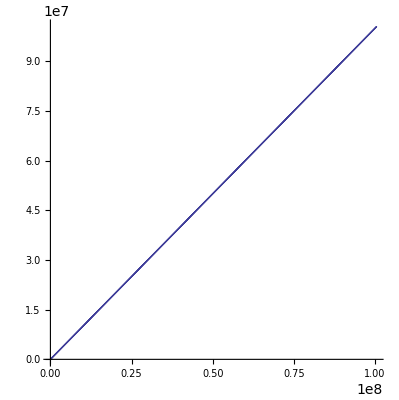

```mathematica
PolarPlot[5/(1+Cos[t-(5π)/4])-2,{t,-π/2,π/2}]
```

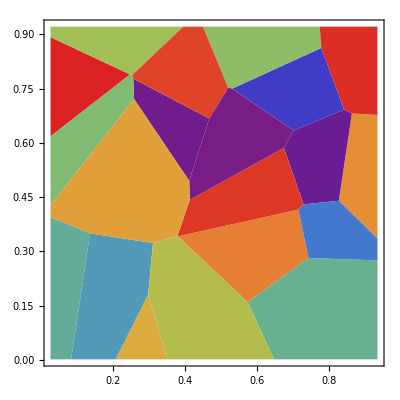

```mathematica
layer0=ListDensityPlot[RandomReal[{},{20,3}],InterpolationOrder->0,Mesh->None,ColorFunction->"Rainbow"]
```

```mathematica
Export["D:/layer0.png",layer0]
```

D:/layer0.png